General::munfl: Exp[-1249.9] is too small to represent as a normalized machine number; precision may be lost.

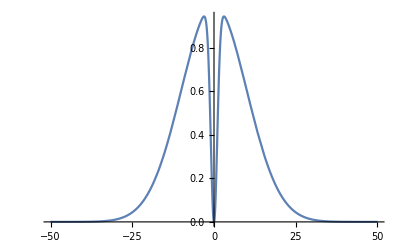

```mathematica
σ1=10;
σ2=1;
RealDensity[r_]:=Exp[-r^2/(2 σ1^2)]-Exp[-r^2/(2 σ2^2)];
Plot[RealDensity[r],{r,-5σ1,5σ1},PlotRange->All]
```

$Aborted

General::munfl: Exp[-1249.9] is too small to represent as a normalized machine number; precision may be lost.

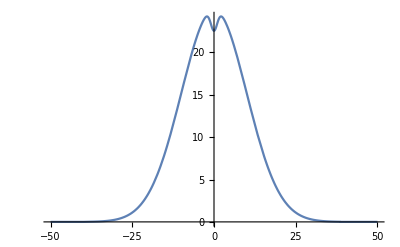

```mathematica
Abel[y_]:=2 Integrate[(RealDensity[r]r)/(√(r^2-y^2)),{r,y,Infinity}];
Plot[Abel[Abs[y]],{y,-5 σ1,5σ1},PlotRange->All]
```

```mathematica
InvAbel[r_]:
```

RealDensity

```mathematica
ClearAll[σ1, σ2]
RealDensity=a1 Exp[(-x^2-y^2)/(2 σ1^2)]-a2 Exp[(-(x-x0)^2-y^2)/(2 σ2^2)];
```